```mathematica
<<VilCretas`
```

VilCretas está disponible.

# Ejercicio 1

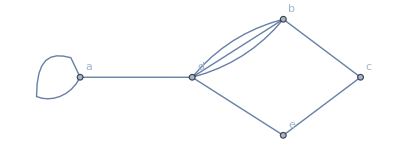

```mathematica
grafo = Grafo[{{a,a},{a,d},{b,c},{b,d},{b,d},{b,d},{c,e},{d,e}}]
```

```mathematica
MIGrafo[grafo,{a,b,c,d,e},table->True]
```

| a<->a | a<->d | b<->c | b<->d | b<->d | b<->d | c<->e | d<->e
a | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
b | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
c | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
d | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
e | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1

# Ejercicio 2

R/

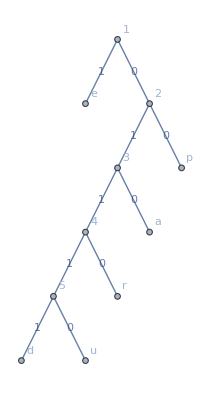

```mathematica
arbolito = ArbolHuffmanN["depauperar"]
```

ruda = 01100111001111010
r =0110
u = 01110
d =01111
a =010

# Ejercicio 3

R/ 200 personas representaran los nodos del grafo, si hay 200 personas incluyendo a Juan, Juan deberá estrechar la mano 200 - 1 = 199 veces.
Para el saludo grupal serian 199 saludos por personas, y son 200 personas, por lo tanto: 19900 saludos se hicieron en esta fiesta grupal

```mathematica
GrafoBipartitoCompleto[200,199, analizar->True];
```

```mathematica
GrafoCompleto[200, analizar->True]
```

# Ejercicio 4

```mathematica
GrafoBipartitoCompleto[10,10,analizar->True]
GrafoCompleto[20,analizar->True]
```

# Ejercicio 5

R/

```mathematica
V={13,66,84,38,10,90,40,21,7};
```

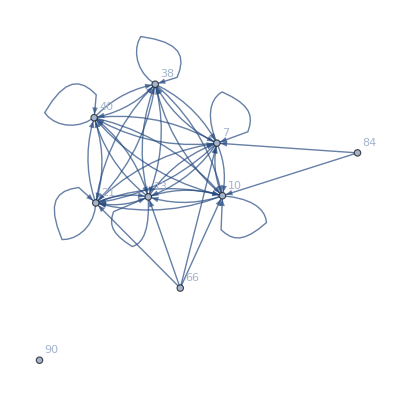

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
Grado o valencia interna | 7 | 0 | 0 | 6 | 8 | 0 | 6 | 7 | 8
Grado o valencia externa | 6 | 4 | 2 | 6 | 6 | 0 | 6 | 6 | 6

```mathematica
R = RelBin["2a+3b<=200",V,V];
grafo =GrafoRelBin[R,V]
Valencias[grafo]
```

# Ejercicio 6

R/

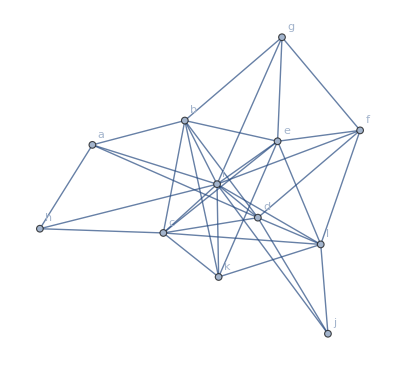

{{{g,i},{i,j}},{{g,f},{f,d},{d,j}},{{g,e},{e,l},{l,j}}}

3

```mathematica
G = Grafo[{{a,b},{a,d},{a,h},{a,i},{b,c},{b,d},{b,e},{b,g},{b,i},{b,k},{c,d},{c,e},{c,h},{c,i},{c,k},{c,l},{d,f},{d,i},{d,j},{d,l},{e,f},{e,g},{e,i},{e,k},{e,l},{f,g},{f,i},{f,l},{g,i},{h,i},{i,j},{i,k},{i,l},{j,l},{k,l}}]
GeneraRutas[G, g,j,5]
Length[%]
```

# Ejercicio 7

R/ El árbol en Mathematica me da diferente por el orden que posee, pero al observarlo bien son el mismo árbol
/*x+xy-x*2+yz

```mathematica
sustitucion ={1->"/",2->"*",3->"*",4->"+",5->"+",6->"-",7->"x",8->"x",9->"y",10->"x",11->"2",12->"y",13->"z"}
```

{1→/,2→*,3→*,4→+,5→+,6→-,7→x,8→x,9→y,10→x,11→2,12→y,13→z}

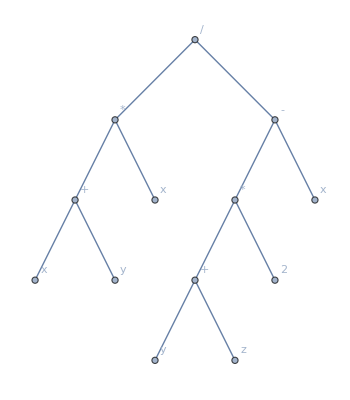

```mathematica
arbolPol = Graph[{{1,2},{1,6},{2,7},{2,4},{4,8},{4,9},{6,3},{3,11},{3,5},{5,12},{5,13},{6,10}}, VertexLabels->sustitucion]
```

```mathematica
StringJoin[Prefijo[arbolPol,1]/.sustitucion]
```

/*+xyx-*+yz2x

/*x + xy*-x2 + yz